# Amoebas

Author: Jens Forsgård
Latest version: June 2020

Thanks to Per Alexandersson, who wrote the first version of the function CoamoebaTrinomial.

```mathematica
BeginPackage[ "Amoebas`"];
Needs["ComputationalGeometry`"];
```

```mathematica
Coamoeba::usage = "Coamoeba[ func] returns a list plot, representing an approximate plot of the coamoeba of the (bivariate) polynomial func.";

CoamoebaTrinomial::usage = "CoamoebaTrinomial[ func] returns a graphic object, representing a plot of the coamoeba of the (bivariate) trinomial func.";

CoamoebaLopsided::usage = "CoamoebaLopsided[ func] returns a graphic object, representing a plot of the lopsided coamoeba of the (bivariate) polynomial func.";

CoamoebaShell::usage = "CoamoebaShell[ func] returns a graphic object, representing a plot of the shell of the coamoeba of the (bivariate) polynomial func.";

CoamoebaSpine::usage = "CoamoebaSpine[ func] returns a graphic object, representing a plot of the phase hyperfield variaty associated with the (bivariate) polynomial func.
N.B., by default, the procedure uses pseudo random numbers for (greatly) improved speed.";

DiscriminantCoamoeba::usage = "DiscriminantCoamoeba[ GaleDual] returns a graphic object, representing a plot of the coamoeba of the reduced (bivariate) discriminant associated with the (N x 2)-matrix GaleDual.";

Amoeba::usage = "Amoeba[ func] returns a list plot, representing an approximate plot of the amoeba of the (bivariate) polynomial func.";

AmoebaLopsided::usage = "AmoebaLopsided[ func] returns a graphics object, representing a plot of the lopsided amoeba of the (bivariate) polynomial func.";
```

```mathematica
Begin["Private`"];
```

## Private Functions

```mathematica
LaurentToPolynomial[func_, arity_] := Module[{z, zz, CoeffRules, ListOfSmallestExponents, Monomial},

	zz = Table[ Symbol["z" <> ToString[k]], {k, 1, arity}];
	CoeffRules = CoefficientRules[func @@ zz, zz];

	(* Check format of input. *)
	If[  Not[AllTrue[ Last /@ CoeffRules,  NumericQ ]],  Return[$Failed]; ];

	(* Construct the monomial representing the shift in exponents. *)
	ListOfSmallestExponents = Min /@  ( (First /@ CoeffRules)ᵀ );
	Monomial = Function[Evaluate[zz], Evaluate[Times @@ (zz^-ListOfSmallestExponents)]];

	Return[ Evaluate[Function[Evaluate[zz], Evaluate[Expand[ (func @@ zz ) * (Monomial @@ zz) ]]]]] ;

];
```

```mathematica
RealPolynomialQ[func_] := Module[{z, w, Coefficients, RealQ},
  
  Coefficients = Last /@ CoefficientRules[func[z, w], {z, w}];
  RealQ[x_] := Not[ Head[x] === Complex ];
  
  AllTrue[Coefficients,  RealQ] // Evaluate // Return;
  
];
```

```mathematica
ExponentialLattice[RadiusRange_, RadiusStep_, AngleRange_, AngleStep_] := Module[{radiusValues, angleValues},
  
  (* Generate all radial respectively angular values. *)
  radiusValues = Table[r, {r, -RadiusRange, RadiusRange, RadiusStep}];
  angleValues  = Table[t, {t, 0, AngleRange, AngleStep}];
  
  (* Return the Cartesian product in exponential coordinates *)
  Return[Flatten[Table[N[Exp[r + I t]], {r, radiusValues}, {t, angleValues}]]];
  
];
```

```mathematica
PointsInVariety[func_, point_] := Module[{points1, points2},

  (* Generate points in the variety by numerical solver. *)
  (* Discard solutions which are too small, as Arg and Log are unstable for values close to zero. *)
  points1 = {#, point} &/@ Select[#[[1,-1]]& /@ NSolve[func[z, point] == 0, z], NumericQ[#] && Abs[#] ≥ 10^-2 &];
  points2 = {point, #} &/@ Select[#[[1,-1]]& /@ NSolve[func[point, w] == 0, w], NumericQ[#] && Abs[#] ≥ 10^-2 &];

  Return[ Join[points1, points2] ];

];
```

## Coamoeba

```mathematica
Options[Coamoeba] = 
	{
	 "PointSize" -> .005, 
	 "PlotColor" -> Purple, 
	 "AngleStep" -> Pi/32, 
	 "RadiusStep" -> 1/4, 
	 "RadiusRange" -> 6, 
	 "AspectRatio" -> 1, 
	 "Axes" -> False
	};

Coamoeba[func_, OptionsPattern[]]:= Module[
	{adjustedfunc, real, AngleRange, lattice, solutions},
	
	Coamoeba::input = "Input function is not a bivariate Laurent polynomial.";

	adjustedfunc = Evaluate[LaurentToPolynomial[func, 2]];
	If[adjustedfunc == $Failed, Message[Coamoeba::input]; Return[$Failed]];
 
	(* Check if the polynomial is real; in which case we can speed up computations. *)
	real = RealPolynomialQ[adjustedfunc];

	If[real, AngleRange = Pi, AngleRange = 2Pi ];
	lattice = ExponentialLattice[OptionValue["RadiusRange"], OptionValue["RadiusStep"], AngleRange, OptionValue["AngleStep"]];
	solutions = Flatten[PointsInVariety[adjustedfunc, #]& /@ lattice, 1];
	If[real, solutions = Join[solutions, Conjugate[solutions]]];

	Return[ListPlot[Arg[solutions], AspectRatio -> OptionValue["AspectRatio"], Axes -> OptionValue["Axes"],
		            PlotRange -> {{-Pi-.025,Pi+.025}, {-Pi-.025,Pi+.025}},
		            PlotStyle -> Directive[OptionValue["PlotColor"], PointSize[OptionValue["PointSize"]]]]];

];
```

## CoamoebaTrinomial

```mathematica
Options[CoamoebaTrinomial] = 
	{
		"PlotColor" -> Purple, 
		"PlotOpacity" -> 1
	};

CoamoebaTrinomial[input_, OptionsPattern[]] := Module[
	{zz, z, coeffRules, exponents, coeffArguments, SubtractFirstFromAll,
	 matrix, constant, Transformation, repetitions, triangle1, triangle2, t1, t2, triangles},

	CoamoebaTrinomial::input = "Input is not a bivariate trinomial.";
	CoamoebaTrinomial::bivariate = "Newton polytope is not two-dimensional."; 

	zz = Table[Indexed[z, k], {k, 1, 2}];
	(* We allow input to be a list of coefficient rules. *)
	If[Head[Evaluate[input]] === Symbol,
		coeffRules = Association[CoefficientRules[input @@ zz, zz]];,
		coeffRules = Association[input];];

	exponents = Keys[coeffRules];
	coeffArguments = Arg[Values[coeffRules]];
 
	If[Length[exponents] ≠ 3, Message[CoamoebaTrinomial::input]; Return[$Failed]];
	If[Not[AllTrue[coeffArguments, NumericQ]],  Message[CoamoebaTrinomial::input]; Return[$Failed]];
 
	(* The algorithm is based on the fact that the coamoeba a linear transformation of the coaoeba 
		of the standard line, when considered in the universal cover. Here, we load the data of the
		inverse linear transformation. *)
	SubtractFirstFromAll[list_] := # - First[list] & /@ Drop[list, 1];
	matrix = SubtractFirstFromAll[exponents];
	If[Det @ matrix == 0, Message[CoamoebaTrinomial::bivariate]; Return[$Failed]];
	constant = Mod[SubtractFirstFromAll[coeffArguments], 2Pi];
	Transformation[object_] := GeometricTransformation[object, InverseFunction[AffineTransform[{matrix,constant}]]];
	
	(* We need to take sufficiently many copies of the comaoeba of the line in the universal cover. *)
	repetitions = Floor[2 + Max[Abs[Eigenvalues[matrix]]]];
	triangle1[t1_,t2_] := Polygon[{{t1-Pi,t2},{t1,t2+Pi},{t1-Pi,t2+Pi}}];
	triangle2[t1_,t2_] := Polygon[{{t1,t2-Pi},{t1+Pi,t2},{t1+Pi,t2-Pi}}];
	triangles = Flatten[Table[{triangle1[t1,t2], triangle2[t1,t2]}, 
							{t1,-2Pi repetitions,2Pi repetitions,2Pi},
							{t2,-2Pi repetitions,2Pi repetitions,2Pi}], 2];

	Graphics[{OptionValue["PlotColor"], Opacity[OptionValue["PlotOpacity"]], Transformation @ triangles}, PlotRange -> Pi] // Return;

];
```

## CoamoebaLopsided

```mathematica
Options[CoamoebaLopsided] = 
	{
		"PlotColor" -> Purple, 
		"PlotOpacity" -> 1
	};

CoamoebaLopsided[func_, OptionsPattern[]]:= Module[
	{z, w, triples, LowerDimensionalQ, trinomials, OneCoamoeba},

	LowerDimensionalQ[cRules_] := Return[Det[Differences[First /@ cRules]] == 0];
	triples = Subsets[CoefficientRules[func[z,w], {z,w}], {3}];
	trinomials = Select[triples, Not[LowerDimensionalQ[#]] &];
	OneCoamoeba[triple_] := CoamoebaTrinomial[triple, "PlotColor" -> OptionValue["PlotColor"], "PlotOpacity" -> OptionValue["PlotOpacity"]];
	Return[Show[OneCoamoeba /@ trinomials]]

];
```

## CoamoebaShell

```mathematica
Options[CoamoebaShell] = 
	{
		"PlotColor" -> Black, 
		"Oriented" -> False, 
		"ArrowSize" -> .025, 
		"ArrowDensity" -> 16, 
		"LineThickness" -> .004
	};

CoamoebaShell[func_, OptionsPattern[]] := Module[
	{ExtremalCoamoeba, z,w, cRules, Exponents, OneDimensionalPolytopeQ, LineList,
	 convexHullIndices, NN, VertexQ, vertexList, OneExtremalPolynomial},

	ExtremalCoamoeba[coeffRules_] := Module[
	(* Internal function: ExtremalCoamoeba
		Input:     The coefficient rules for the extremal polynomial of one of the edges of the Newton polytope
		Output:    The coamoeba of the extremal polynomial as a set of (possibly oriented) lines *)

		{vector, M, univariateExponents, k, univariatePolynomial, FindOnePoint, ArgumentList},
		
		(* Retrieve the tangent vector of the Newton polytope *)
		vector =  First /@ Take[coeffRules,2] // Differences // First;
		(* And reduce it to a primitive integer vector *)
		vector = vector / (GCD@@vector);
		
		(* The number of fundamental domain which we must consider is relative the size of the entries of the tangent vector *)
		M = Max[Abs[vector]];
		
		(* Retrieve the list of exponents of the univariate polynomial. *)
		univariateExponents = Flatten[(k/.Solve[coeffRules[[1,1]] + k vector ==  First[#], k]) & /@ coeffRules];
		(* Construct the univariate polynomial. *)
		univariatePolynomial[z_] := Evaluate[ Dot[ Last/@ coeffRules, z^univariateExponents ] ];
		
		(* Find the arguments of the roots of the univaraite polynomial... *)
		ArgumentList = Arg[z/. NSolve[univariatePolynomial[z] == 0, z]];
		(* ...and extend to a list of roots in 2M many fundamental domains. *)
		ArgumentList = Flatten[Table[a+l 2Pi, {l,-M,M}, {a, ArgumentList}]];
		(* Translate ArgumentList to a list of points on the 2-torus. *)
		FindOnePoint[arg_]:=If[First[vector]≠0, Return[{arg/First[vector], 0}];, Return[{0, arg/Last[vector]}]];
		ArgumentList = FindOnePoint /@ ArgumentList;
		
		(* The tangent vector of the line is orthogonal to the tangent vector of the Newton polytope. *)
		vector = vector . {{0,1},{-1,0}};
		
		(* Return a set of lines with display properties according to option values. *)
		If[ Not[OptionValue["Oriented"]],
			Return[Line[{# - 2 Pi vector, # + 2Pi vector}] &/@ ArgumentList];,
			Return[Table[Arrow[{# - 2 Pi vector + 4 Pi vector k / (OptionValue["ArrowDensity"]M), # - 2 Pi vector + 4 Pi vector (k+1)/(OptionValue["ArrowDensity"]M)}], {k,0,OptionValue["ArrowDensity"]M-1}]&/@ ArgumentList];
		];
	];

	(* Retrieve the coefficient rules *)
	cRules = CoefficientRules[func[z,w], {z,w}];
	Exponents = First /@ cRules;

	OneDimensionalPolytopeQ[points_] := Return[MatrixRank[Prepend[pointsᵀ, ConstantArray[1, Length[cRules]]]]==2];

	If[OneDimensionalPolytopeQ[Exponents],
		
		(* If the polytope is one dimensional, then there is only one set of lines. *)
		LineList = ExtremalCoamoeba[cRules];,
		
		(* Else, there are several sets of lines. *)
		(* Retrieve the indices of the points on the boundary of the Newton polytope *)
		convexHullIndices = ConvexHull[Exponents];
		NN = Length[convexHullIndices];
		
		(* Retrieve the indices which label vertices of the Newton polytope *)
		VertexQ[ind_]:= Module[{thisPoint, nextPoint, previousPoint, differenceMatrix},
			thisPoint        = convexHullIndices[[ind]];
			nextPoint        = convexHullIndices[[If[ind == NN, 1, ind + 1]]];
			previousPoint    = convexHullIndices[[If[ind == 1, NN, ind - 1]]];
			differenceMatrix = {Exponents[[thisPoint]] - Exponents[[nextPoint]], Exponents[[thisPoint]] - Exponents[[previousPoint]]};
			Return[Not[Det[differenceMatrix]==0]];
		];
		vertexList = Select[Range[NN], VertexQ];
		
		(* For simpler indexing, adjust vertexList and convexHullIndices *)
		vertexList = Append[vertexList, First[vertexList] + NN];
		convexHullIndices = Join[convexHullIndices, convexHullIndices];
		
		(* OneExtremalPolynomial retrieves the extremal polynomial whose first monomial is vertex no. _ind_ *)
		OneExtremalPolynomial[ind_] := cRules[[#]]& /@ convexHullIndices[[  vertexList[[ind]];;vertexList[[ind+1]]  ]];
		
		(* Create the list of lines. *)
		LineList = Flatten[ExtremalCoamoeba /@ (OneExtremalPolynomial /@ Range[Length[vertexList]-1]) ];
	];
	
	(* Return a plot of all lines in the list with display properties as described by option values *)
	Return[Graphics[
		{
			OptionValue["PlotColor"],
			Arrowheads[OptionValue["ArrowSize"]],
			Thickness[OptionValue["LineThickness"]], 
			LineList
		},
		PlotRange -> {{-Pi- .025, Pi+.025},{-Pi-.025, Pi+.025}}]
	];
];
```

## CoamoebaSpine

```mathematica
Options[CoamoebaSpine] = 
	{
		"PlotColor" -> Black,
		"LineThickness" -> .007,
		"UseRandomNumber" -> False
	};

CoamoebaSpine[func_, OptionsPattern[]] := Module[
	{ArgumenLinearForms, IntermediateAnglesList, ConstructListOfForms, 
	TriplesOfLinearForms, FindPoints, TestVertexPoint, PossibleVertices,
	ExtendedPossibleVertices, TestTropPoint, PossiblePairs, mm, TestIntermediateMinPoint,
	TestIntermediatePoint, t1, t2, z, w},

	(* Retrieve the list of linear forms describing how the arguments of the monomials depend on the arguments of the variables *)
	ArgumenLinearForms = First[#].{t1,t2} + Arg[Last[#]] & /@ CoefficientRules[func[z, w], {z, w}];
	(* Retrieve the list of angles between two monomials; with respect to both orientations *)
	IntermediateAnglesList = Flatten[{First[#] - Last[#], Last[#] - First[#]} & /@ Subsets[ArgumenLinearForms, {2}]];

	(* Extend the list of intermediate angles across sufficiently many fundamental domains *)
	ConstructListOfForms[form_] := Module[{qList, m, M},
		qList = Quotient[(form/.{t1->First[#], t2->Last[#]}), 2Pi]& /@ {{0,0}, {0,2Pi}, {2Pi,0}, {2Pi,2Pi}};
		m = -Max[qList];
		M = -Min[qList];
		Return[Table[form+2Pi k, {k,m,M}]];
	];
	IntermediateAnglesList = Flatten[ConstructListOfForms /@ IntermediateAnglesList];

	(* Collect all triples of linear forms. *)
	TriplesOfLinearForms = Subsets[IntermediateAnglesList, {3}];

	FindPoints[triple_]:=Module[{coeffList, AList={}, BList={}, CList={}, DList={}, totalList}, 
		(* Retrieve the coefficients of the variables in the triple of linear forms *)
		coeffList = {D[#,t1], D[#,t2]}& /@ triple;
		(* There are four possibilities for intersection points, dependin on which two monomial are aligned *)
		If[Det[Differences[coeffList]]≠0, 
			AList = Solve[Differences[triple] ==0, {t1,t2}];];
		If[Det[{coeffList[[1]], coeffList[[2]]-coeffList[[3]]}]≠0,
			BList = Solve[{triple[[1]] ==0, triple[[2]]==triple[[3]]}, {t1,t2}];];
		If[Det[{coeffList[[2]], coeffList[[1]]-coeffList[[3]]}]≠0,
			CList = Solve[{triple[[2]] ==0, triple[[1]]==triple[[3]]}, {t1,t2}];];
		If[Det[{coeffList[[3]], coeffList[[1]]-coeffList[[2]]}]≠0,
			DList = Solve[{triple[[3]] ==0, triple[[1]]==triple[[2]]}, {t1,t2}];];
		(* Joine the four lists of possible points *)
		totalList = Join[AList, BList, CList, DList];
		(* Return only the points which lies in the standard fundamental domain *)
		If[Length[totalList] ==  0, 
			Return[{}];,
			Return[ Select[{t1,t2}/.totalList, First[#]≥0 && First[#]< 2Pi && Last[#]≥0 && Last[#]<2Pi &]];
		];
	];
	
	(* Retrieve the list of all possible vertices of the spine. *)
	PossibleVertices = DeleteDuplicates[Flatten[FindPoints/@TriplesOfLinearForms,1]];

	(* Test if a given point is a vertex or not, and filter the list of possible vertices. *)
	TestVertexPoint[th_]:=Module[{inList, dList},
		inList = Sort[Mod[ArgumenLinearForms/.{t1->First[th], t2->Last[th]},2Pi]];
		dList = Differences[Append[inList, 2Pi + First[inList]]];
		If[Last[First[Tally[Sort[dList, #1>#2&]]]] > 2, 
			Return[True];, 
			If[Last[First[Tally[Sort[dList, #1>#2&]]]]> 1 && Last[Sort[dList, #1>#2&]]==0,
				Return[True];,
				Return[False];
			];
		];
	];
	PossibleVertices = Select[PossibleVertices, TestVertexPoint[#]&];
	
	(* Extend the list of possible vertices to adjacent fundamental domains. *)
	ExtendedPossibleVertices = Select[Flatten[Table[#+2Pi{k1,k2},{k1,-2,1}, {k2,-2,1}]&/@PossibleVertices,2], #[[1]]≥ -3Pi&&#[[1]]≤ 3Pi && #[[2]]≥-3Pi&&#[[2]]≤ 3Pi&];

	(* Find all possible lines and to a first filtering based on whether the midpoint point is in the spine... *)
	TestTropPoint[th_]:=Module[{inList, dList},
		inList = Sort[Mod[ArgumenLinearForms/.{t1->First[th], t2->Last[th]},2Pi]];
		dList  = Differences[Append[inList, 2Pi + First[inList]]];
		If[Last[First[Tally[Sort[dList, #1>#2&]]]] > 1, Return[True], Return[False]];
	];
	PossiblePairs = Subsets[ExtendedPossibleVertices, {2}];
	PossiblePairs = Select[PossiblePairs, Max[Abs[Differences[#]]] < 2Pi&];
	PossiblePairs = Select[PossiblePairs,TestTropPoint[Total[#]/2]&];
	
	If[OptionValue["UseRandomNumber"],
		(* ... and do a second filtering based on whether a random intermediate point is in the spine. *)
		TestIntermediatePoint[pair_]:=Module[{r}, 
			r = Rationalize[Random[], 1/1000];
			Return[TestTropPoint[r pair[[1]] + (1-r)pair[[2]]]];
		];
		PossiblePairs=Select[PossiblePairs,TestIntermediatePoint[#]&];
	];
	
	(* ... and do a third filtering based on whether a 'minimal distance from vertex' point is in the spine *)
	mm = Min[Norm/@(First/@(Differences/@Subsets[PossibleVertices,{2}]))]/2;
	TestIntermediateMinPoint[pair_]:=Module[{kk,TList},
		kk = Quotient[Norm[pair[[2]]-pair[[1]]], mm];
		TList =Table[ pair[[1]] +(pair[[2]]-pair[[1]])k/kk, {k,1,kk-1}];
		If[Length[TList] == 0, Return[False],Return[First[Sort[TestTropPoint/@TList]]]];
	];
	PossiblePairs = Select[PossiblePairs, TestIntermediateMinPoint];
	
	(* Plot the set of lines which remains. *)
	Return[Show[Graphics[{OptionValue["PlotColor"], Thickness[OptionValue["LineThickness"]], Line[#]}, PlotRange->{{-Pi,Pi}, {-Pi,Pi}}]&/@PossiblePairs]];
];
```

## DiscriminantCoamoeba

```mathematica
Options[DiscriminantCoamoeba] = 
	{
		"PlotColor" -> Gray,
		"BoundaryColor" -> Black, 
		"BoundaryThickness" -> .0025,
		"PlotOpacity" -> .5
	};

DiscriminantCoamoeba[GaleDual_, OptionsPattern[]] := Module[
	{AdjustedGaleDual, k, indicators, row, tempMatrix, cycleVertices, 
	multiple, shifts, polygons,polygons1,polygons2, t, point, translation, NormalSlope},

	DiscriminantCoamoeba::input    = "Input is not a homogeneous full rank Nx2 matrix.";
	DiscriminantCoamoeba::adjusted = "Input matrix has been adusted for parallel and zero rows.";
	DiscriminantCoamoeba::parallel = "Input has parallel rows; replacing them by their sum.";

	AdjustedGaleDual = Select[GaleDual, # ≠ {0,0} &];

	(* Gather parallel rows *)
	k = 1;
	While[k ≤ Length[AdjustedGaleDual],
		indicators  = (Det[{AdjustedGaleDual[[k]], #}] == 0) & /@ AdjustedGaleDual;
		If[ Count[indicators, True] > 1,
			row = Total[ AdjustedGaleDual[[ Flatten[ Position[indicators, True] ] ]] ];
			AdjustedGaleDual = AdjustedGaleDual[[ Flatten[ Position[indicators, False] ] ]];
			If[ row ≠ {0,0}, AdjustedGaleDual = Insert[ AdjustedGaleDual, row, k]; ];
		];
		k = k + 1;
	];

	(* Warn in case the Gale dual has been adjusted *)
	If[Length[AdjustedGaleDual] ≠ Length[GaleDual], Message[DiscriminantCoamoeba::adjusted];];
	
	(* Input format check. *)
	If[Length[First[AdjustedGaleDual]] ≠ 2, Message[DiscriminantCoamoeba::input]; Return[$Failed]];
	If[MatrixRank[AdjustedGaleDual] ≠ 2, Message[DiscriminantCoamoeba::input]; Return[$Failed]];
	If[Total[AdjustedGaleDual] ≠ {0,0}, Message[DiscriminantCoamoeba::input]; Return[$Failed]];
	
	(* Order the rows by their normal slopes. *)
	NormalSlope[β_] := Module[{},
		If[ Last[β] == 0, 
			Return[ -Sign[First[β]] * Infinity ];,
			Return[ -First[β] / Last[β] ];
		];
	];
	AdjustedGaleDual = Sort[AdjustedGaleDual, NormalSlope[#1] > NormalSlope[#2] &];
	
	(* Retrieve the vertices of the basic cyclce as partial sums *)
	cycleVertices = Prepend[Total[AdjustedGaleDual[[1 ;; #]]] & /@ Range[Length[AdjustedGaleDual]], {0,0}];
	
	(* Compute the set of all shifts of the cycle neccessary to get the correct picture *)
	multiple = 2*Ceiling[Max[Abs[Flatten[cycleVertices]]]/2];
	shifts = Flatten[Table[{k1,k2}, {k1,-multiple, multiple, 2}, {k2, -multiple, multiple, 2}], 1];
	
	(* Compute the translation of the cycle *)
	point = Max[Flatten[(t/.Solve[# == 0, t])& /@ Select[AdjustedGaleDual.{1,t}, Not[NumericQ[#]]&]]] + 1;
	translation = Arg[Times@@# &/@(((AdjustedGaleDual.{1, point})^AdjustedGaleDual)ᵀ)];
	
	(* Rescale and shift; adjoin mirrored cycles *)
	polygons1 = Table[ (translation + Pi*(# + shift)) & /@ cycleVertices, {shift, shifts} ];
	polygons2 = Table[ (translation - Pi*(# + shift)) & /@ cycleVertices, {shift, shifts} ];
	polygons = Join[polygons1, polygons2];
	
	(* Return the graphics element *)
	Return[
		Graphics[
		{
			OptionValue["PlotColor"], 
			Opacity[OptionValue["PlotOpacity"]], 
			Polygon /@ polygons,
			Opacity[1], 
			Thickness[OptionValue["BoundaryThickness"]],
			OptionValue["BoundaryColor"], 
			Line /@ polygons
		}, PlotRange -> {{-Pi-.015,Pi+.015},{-Pi-.015,Pi+.015}}
		]
	];

];
```

## Amoeba

```mathematica
Options[Amoeba] = 
	{
		"PointSize" -> .005, 
		"PlotColor" -> Purple, 
		"AngleStep" -> Pi/32, 
		"RadiusStep" -> 1/4, 
		"RadiusRange" -> 6, 
		"AspectRatio" -> 1, 
		"Axes" -> False
	};

Amoeba[func_, OptionsPattern[]]:= Module[
	{adjustedfunc, real, angleRange, lattice, solutions, LogAbs},

	Amoeba::input = "Input function is not a bivariate Laurent polynomial.";

	adjustedfunc = LaurentToPolynomial[func, 2];

	(* Check whether adjustedfunc has the expected form. If not, abort. *)
	If[adjustedfunc == $Failed, Message[Amoeba::input]; Return[$Failed]];

	(* Check if the polynomial is real; in which case we can speed up computations. *)
	real = RealPolynomialQ[adjustedfunc];

	If[ real, angleRange = Pi, angleRange = 2Pi ];
	lattice = ExponentialLattice[OptionValue["RadiusRange"], OptionValue["RadiusStep"], angleRange, OptionValue["AngleStep"]];

	(* Create a list of points in the variety. *)
	solutions = Flatten[PointsInVariety[adjustedfunc, #]& /@ lattice, 1];

	(* If the variety is real, join with the conjugate solutions. *)
	If[real, solutions = Join[solutions, Conjugate[solutions]]];
	
	LogAbs[x_] := Log[Abs[x]];
	
	(* Return the ListPlot with parameters. *)
	Return[ListPlot[LogAbs[solutions], AspectRatio -> OptionValue["AspectRatio"], Axes -> OptionValue["Axes"], PlotRange -> {{-Pi-.025, Pi+.025},{-Pi-.025, Pi+.025}},PlotStyle -> Directive[OptionValue["PlotColor"],PointSize[OptionValue["PointSize"]]]]];

];
```

## AmoebaLopsided

```mathematica
Options[AmoebaLopsided] = 
	{
		"AmoebaColor" -> LightGray, 
		"BorderColor" -> Black, 
		"BorderWidth" -> .004, 
		"MaxRecursion" -> 5, 
		"PlotRange" -> {{-4,4},{-4,4}}
	};
	
AmoebaLopsided[func_, OptionsPattern[]]:= Module[
{z, w, coefficientRules, MakePolynomial, polynomials, plotRange},

	(* Retrieve the coefficient rules for the polynomial obtained by taking absolute values of the coefficients *)
	coefficientRules = {First[#], Abs[Last[#]]} & /@ CoefficientRules[func[z,w],{z,w}];
	
	(* Internat function MakePolynomial creates a polynomial from a list of coefficient rules *)
	MakePolynomial[cRules_] := Total[Last[#] Times@@({Exp[z],Exp[w]}^First[#]) &/@ cRules];
	
	(* Each boundary component of the lopsided amoeba is the line defined by switching the sign of one monomial *)
	polynomials = MakePolynomial/@ (ReplacePart[coefficientRules, {#,2} -> -coefficientRules[[#,2]]] & /@ Range[Length[coefficientRules]]);
	
	(* Set plotRange vectore *)
	plotRange = Flatten/@({{z,w}, OptionValue[PlotRange]}ᵀ);
	
	(* Return the region plot and one contour plot for each boundary piece. *)
	Return[Show[Prepend[
			ContourPlot[#==0, plotRange[[1]], plotRange[[2]], Frame->None, ContourStyle -> Directive[OptionValue["BorderColor"], Thickness[OptionValue["BorderWidth"]]]] & /@ polynomials, 
			RegionPlot[And @@ (# > 0 &/@ polynomials), plotRange[[1]], plotRange[[2]], PlotStyle -> OptionValue["AmoebaColor"], BoundaryStyle->None, Frame->None, MaxRecursion -> OptionValue[MaxRecursion]]
		   ]]
	];
];
```

```mathematica
End[];
EndPackage[];
```

Examples

## Coamoeba

{PointSize→0.005,PlotColor→RGBColor[0.5, 0, 0.5],AngleStep→π/32,RadiusStep→1/4,RadiusRange→6,AspectRatio→1,Axes→False}

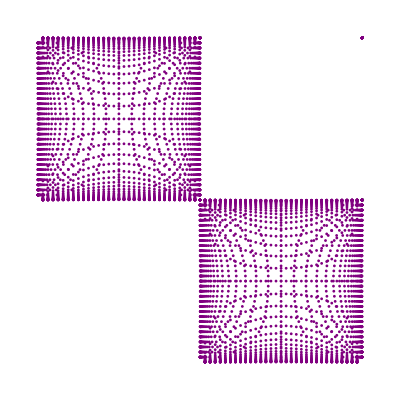
{4.48751,-Graphics-}

```mathematica
f[z_,w_]:= 1 + z + w- z w;
Options[Coamoeba]
Timing[Coamoeba[f]]
```

## CoamoebaTrinomial

{PlotColor→RGBColor[0.5, 0, 0.5],PlotOpacity→1}

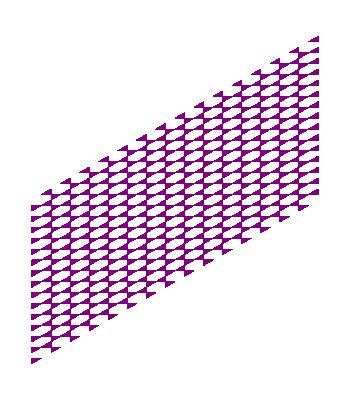
{0.006473,-Graphics-}

{0.005497,-Graphics-}

```mathematica
f[z_,w_]:= 1 - z^4 + w^7;
Options[CoamoebaTrinomial]
Timing[CoamoebaTrinomial[f]]
Timing[CoamoebaTrinomial[CoefficientRules[f[z,w], {z,w}]]]
```

## CoamoebaLopsided

{PlotColor→RGBColor[0.5, 0, 0.5],PlotOpacity→1}

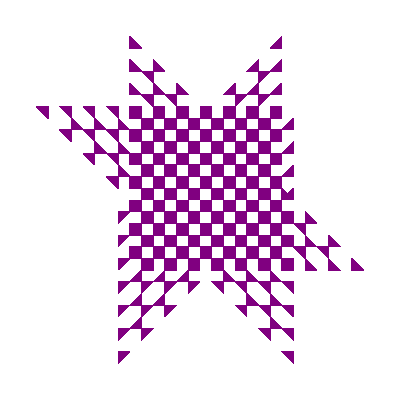
{0.009208,-Graphics-}

```mathematica
f[z_,w_]:= 1 + z + w- z w;
Options[CoamoebaLopsided]
Timing[CoamoebaLopsided[f]]
```

## CoamoebaShell

{PlotColor→GrayLevel[0],Oriented→False,ArrowSize→0.025,ArrowDensity→16,LineThickness→0.004}

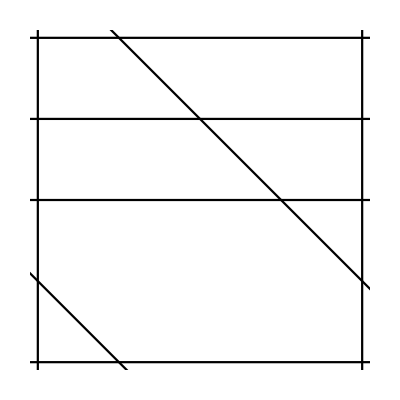
{0.013323,-Graphics-}

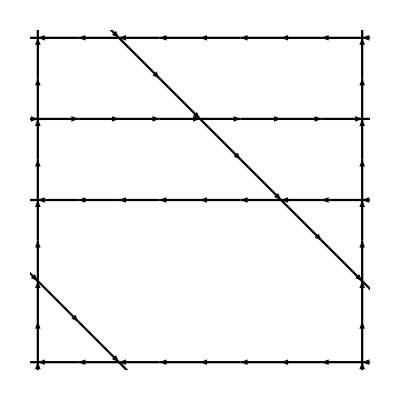
{0.018919,-Graphics-}

```mathematica
f[z_,w_]:= 1 + z +I  w- z w^2;
Options[CoamoebaShell]
Timing[CoamoebaShell[f]]
Timing[CoamoebaShell[f, Oriented -> True]]
```

## CoamoebaSpine

{PlotColor→GrayLevel[0],LineThickness→0.007,UseRandomNumber→False}

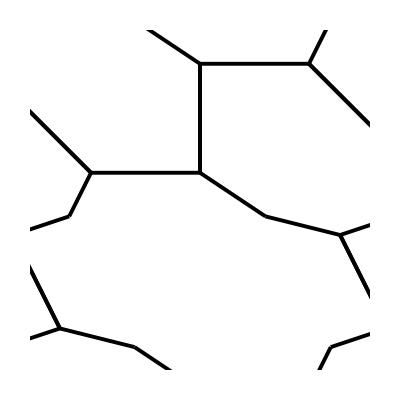
{5.39225,-Graphics-}

{5.38919,-Graphics-}

```mathematica
f[z_,w_]:= 1 + z +I  w- z w^2;
Options[CoamoebaSpine]
Timing[CoamoebaSpine[f]]
Timing[CoamoebaSpine[f, UseRandomNumber -> True]]
```

## DiscriminantCoamoeba

```mathematica
A = {{1,1,1,1},{0,1,2,3}};
B = {{2,1},{-3,-2},{0,1},{1,0}};
DD[x1_,x2_]:= Evaluate[GroebnerBasis[Numerator[Factor[Times@@# &/@(((B.{1,t})^B)ᵀ) - {x1,x2}]], {x1,x2},{t}][[1]]]
```

{PlotColor→GrayLevel[0.5],BoundaryColor→GrayLevel[0],BoundaryThickness→0.0025,PlotOpacity→0.5}

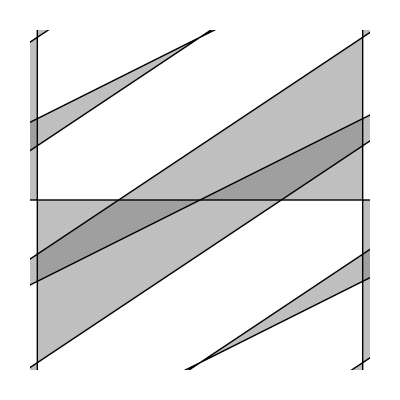
{0.00247,-Graphics-}

```mathematica
Options[DiscriminantCoamoeba]
Timing[DiscriminantCoamoeba[B]]
```

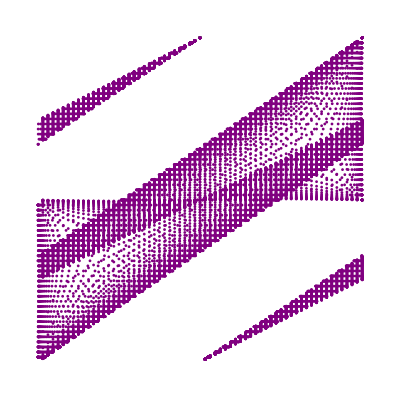
{-Graphics-,-Graphics-}

```mathematica
{Coamoeba[DD], DiscriminantCoamoeba[B]}
```

## Amoeba

{PointSize→0.005,PlotColor→RGBColor[0.5, 0, 0.5],AngleStep→π/32,RadiusStep→1/4,RadiusRange→6,AspectRatio→1,Axes→False}

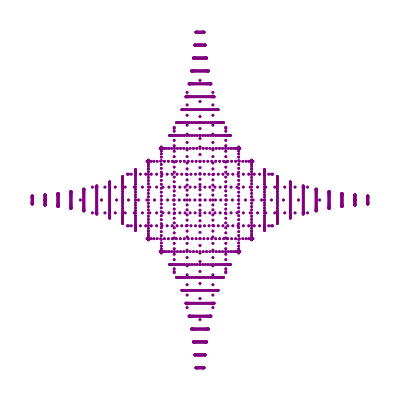
{4.52993,-Graphics-}

```mathematica
f[z_,w_]:= 1 + z + w- z w;
Options[Amoeba]
Timing[Amoeba[f]]
```

## AmoebaLopsided

{AmoebaColor→GrayLevel[0.85],BorderColor→GrayLevel[0],BorderWidth→0.004,MaxRecursion→5,PlotRange→{{-4,4},{-4,4}}}

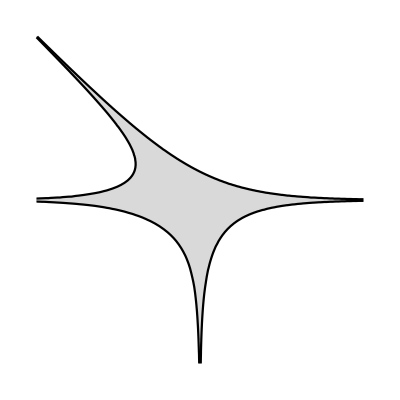
{0.66532,-Graphics-}

```mathematica
f[z_,w_]:= 1 + z +I  w- z w^2;
Options[AmoebaLopsided]
Timing[AmoebaLopsided[f]]
```